```mathematica
(* constants*)
(*https://en.wikipedia.org/wiki/Avogadro_constant*)
N0=6.02214076*10^23;
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
(*Positron lifetime*)
tpo=0.4787*10^(-9);
(*Bohr radius*)
rb=5.29*10^(−9);
(*single monopole charge*)
Qm=2*Pi*hbar/e;
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
Clear[Ql]
Ql=Table[Ql/.Solve[ml[[i]]==(8*Pi/3)*Ql^3,Ql][[3]],{i,3}]
α=1/137.035999206;
αw=0.42541281596347497;
(*From:https://en.wikipedia.org/wiki/Fermi%27s_interaction*)
Gf=1.4327038609285911*^-49;
Ω=0.0078749969978123844;
kb=1.380658*10^(-16);
omega=0.00787499699;
(*calculated already unified*)
mH=126.22136632802759*10^3*me/mev;
mp=1.672621777*10^(-24);
mn=1838.6402*me;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
θwrad=ArcSin[Sqrt[0.231208]];
θwdeg=θwrad*180/Pi;
(*https://en.wikipedia.org/wiki/Precision_tests_of_QED*)
g=2*1.00115965218085;
(* unification mass:anti-deSitter model*)
muni=3.6543166832631125*^-12;
mtau=1776.82*me/mev;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=125.38*10^3*me/mev;
mz=91.1876*10^3*me/mev;
mw=80.4335*10^3*me/mev;
mtop=172.93*10^3*me/mev;
mbottom=4.1*10^3*me/mev;
mcharm=1.275*10^3*me/mev;
mtb=179.3*10^3*me/mev;
mstrange=92.4*me/mev;
momegassb=6054.4/10^3;
mplanck=Sqrt[hbar*c/G];
mup=2.01*me/mev;
md0=4.79*me/mev;
mq1=613.7092426837784*me;
mq2=611.2217146324427*me;
(* log linear fit for 4th level quarks*)
mwhite=1.1677931388727855*^-19;
mblack=1.8611487827001873*^-22;
mout=1.5020666505936996*^-20;
Tvac=2.72548;
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2;
rplanck=2*Pi*hbar/(mplanck*c);
tplanck=rplanck/c;
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
mnu=1.78266270 * 10^(-33 );
mnumu=6.7978246932973695*^-31;
mnutau=1.1431743145263108*^-29;
```

Part::partd: Part specification 2.26146×10^-39⟦1⟧ is longer than depth of object.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partd: Part specification 2.26146×10^-39⟦2⟧ is longer than depth of object.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partd: Part specification 2.26146×10^-39⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{1/2 (-1)^(2/3) (3/π)^(1/3) (2.26146×10^-39⟦1⟧)^(1/3),1/2 (-1)^(2/3) (3/π)^(1/3) (2.26146×10^-39⟦2⟧)^(1/3),1/2 (-1)^(2/3) (3/π)^(1/3) (2.26146×10^-39⟦3⟧)^(1/3)}

```mathematica
(*New universe age: Some Old Globular Clusters (and Stars) Inferring That the
Universe Is Older Than Commonly Accepted
Félix Llorente de Andrés*)
tun=26.7*10^9*365.25*24*60*60;
run=c*tun;
```

```mathematica
(*Weak charge on 5d simplex*)
Cw=(3!*2!)*Det[{{α,0,0,0,0,1},{0,α,0,0,0,1},{0,0,α,0,0,1},{0,0,0,α,0,1},{0,0,0,0,α,1},{0,0,0,0,0,1}}]/5!;
rw=Cw^2/(mnu*c^2);
(*http://www.bottomlayer.com/bottom/deutsch/neutrino.html*)
(* Weeks volume*)
vw=0.94270736277692772092;

(* Thurston-Meyerhoff volume*)
vt=0.981368828892232088914;
(*lepton hyperbolic 3 manifold volume*)
vl=(18/24)*vt;
pizero=134.9766*me/mev;
(* Bohr radius: https://en.wikipedia.org/wiki/Bohr_radius*)
ab=5.2917721067*10^(-9);
(*:https://en.wikipedia.org/wiki/Pion:*)
tpip=2.6033*10^(−8 );
tpiz=8.4*10^(−17);
(* product quarks masses in me*)
mup1=12.239779918021176;mdp1=12.256361761325056;
(* elliptic product quarks for Pi mesons*)
mupi=16.25229214603282;mdpi=16.805755043381577;
mqmu=Sqrt[mmu/me];
mqtau=Sqrt[mtau/me];
(* hadron strange and charm product quark masses*)
mqs=mqtau*mup1/mqmu;
mqc=2*mqs;
ttau=2.932*10^(−13);
tmu=2.1969811*10^(−6);
(*.10https://physicstoday.scitation.org/doi/10.1063/PT.3.4424*)
(*.10https://physics.stackexchange.com/questions/134856/units-of-hubble-time-and-hubble-constant*)
Hcbm=67.4/(3.09*10^19);
Hsnova=74.0/(3.09*10^19);
Hlense=73.3/(3.09*10^19);
Have=73.8/(3.09*10^19);
H0=2.2894835758225842*^-18;
th0=1/H0;
(* CMB age*)
tcmb=372000*365.25*24*60*60;
tsnova=1/Hsnova;
msun=1.9891*10^33;
(*first approximation electron g:single loop GED:weak g'*)
g0=2*(1+α/2);
Clear[g1]
g1=g1/.Solve[(g1/Sqrt[g+g1^2])^2==0.231208,g1][[2]];
(* gravity momemt γ*)
γ=e*G/(hbar*c);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Clear[v,a0,b0,c0,d0,n]
```

```mathematica
v={a0,b0,c0,d0}={1/2,1/3,1/Prime[n],(Prime[n]-6)/(6*Prime[n])}
```

{1/2,1/3,1/Prime[n],(-6+Prime[n])/(6 Prime[n])}

```mathematica
w=Apply[Plus,v]
```

5/6+1/Prime[n]+(-6+Prime[n])/(6 Prime[n])

```mathematica
Table[If[FullSimplify[w]==1,Prime[n],Nothing],{n,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
z=Table[If[FullSimplify[w]==1,{1/2,1/3,1/Prime[n],(-6+Prime[n])/(6 Prime[n])},Nothing],{n,100}];
```

```mathematica
(* Fuchsian triangle group projected on the uncertainty vacuum*)
```

```mathematica
w0[i_]:={ΔE^z[[i,1]]*Δt^z[[i,2]]*Δp^z[[i,3]]*Δr^z[[i,4]]-hbar==0/.ΔE->Δp/c/.Δr->c*Δt}
```

```mathematica
m[i_]:=Abs[Δp/c]/.Solve[w0[i],{Δt,Δp}][[1]]/.Δt->Sqrt[hbar/(c)]
```

```mathematica
ml=Last[Table[m[i],{i,100}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

$Aborted

```mathematica
ml*c^4*10*α^2
```

0.972751

```mathematica
Prime[6]
```

13

```mathematica
u=Table[m[i]/(kb*Tvac/c^2),{i,100}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

{4.5191×10^7,452704.,2349.48,126.361,5.42768,2.11113,0.579862,0.36551,0.18124,0.0888576,0.0742204,0.0483186,0.038792,0.0352707,0.0298455,0.0243142,0.020623,0.0196581,0.0173122,0.0160916,0.0155594,0.014207,0.0134671,0.0125388,0.0115545,0.0111446,0.0109565,0.0106095,0.0104493,0.0101521,0.00930729,0.00910964,0.00884146,0.00875878,0.0083881,0.00832151,0.00813468,0.00796518,0.00786068,0.00771522,0.00758183,0.0075398,0.00734579,0.00730994,0.00724089,0.00720764,0.00702402,0.00686395,0.00681506,0.00679138,0.00674546,0.00667999,0.00665902,0.00656004,0.00650497,0.00645282,0.00640338,0.00638746,0.0063413,0.00631179,0.0062974,0.00622881,0.00614136,0.00611802,0.0061066,0.00608426,0.00601088,0.00598154,0.00593517,0.00592626,0.00590877,0.00588335,0.00585091,0.0058276,0.00580511,0.00579056,0.00576935,0.00574217,0.00572904,0.00570362,0.00567335,0.00566749,0.00563907,0.00563356,0.00561736,0.00560683,0.00559142,0.00557156,0.00556191,0.00555716,0.00554778,0.00552068,0.00550341,0.00549501,0.00547865,0.00547068,0.00545898,0.00543646,0.00543282,0.00540133}

```mathematica
u/α
```

{6.19279×10^9,6.20368×10^7,321963.,17316.,743.787,289.3,79.4619,50.0881,24.8364,12.1767,10.1709,6.62138,5.3159,4.83335,4.08991,3.33192,2.82609,2.69387,2.3724,2.20513,2.1322,1.94687,1.84547,1.71827,1.58338,1.52721,1.50143,1.45389,1.43193,1.39121,1.27543,1.24835,1.2116,1.20027,1.14947,1.14035,1.11474,1.09152,1.0772,1.05726,1.03898,1.03322,1.00664,1.00173,0.992263,0.987706,0.962543,0.940608,0.933909,0.930663,0.924371,0.915399,0.912525,0.898961,0.891415,0.884269,0.877493,0.875312,0.868987,0.864943,0.86297,0.853572,0.841587,0.838389,0.836824,0.833763,0.823707,0.819686,0.813332,0.812111,0.809714,0.806231,0.801786,0.798591,0.795509,0.793515,0.790608,0.786884,0.785084,0.781601,0.777453,0.77665,0.772755,0.772,0.76978,0.768337,0.766225,0.763504,0.762182,0.76153,0.760245,0.756531,0.754166,0.753015,0.750773,0.749681,0.748077,0.744991,0.744492,0.740176}

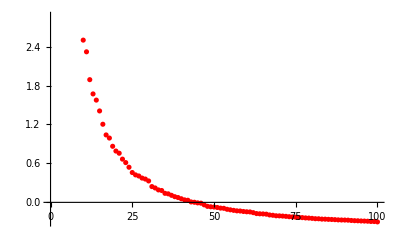

```mathematica
g0=ListPlot[Log[u/α],PlotStyle->Red]
```

```mathematica
f[x_]=Fit[Log[u/α],Join[Table[x^n,{n,0,25}],{Log[x]}],x]
```

58.1555-43.4395 x+9.00292 x^2-1.28955 x^3+0.127495 x^4-0.0089095 x^5+0.00044768 x^6-0.0000162746 x^7+4.24211×10^-7 x^8-7.65242×10^-9 x^9+8.61844×10^-11 x^10-3.81794×10^-13 x^11-3.73728×10^-15 x^12+5.21429×10^-17 x^13+1.06543×10^-19 x^14-4.51529×10^-21 x^15-3.17523×10^-24 x^16+3.73906×10^-25 x^17+1.99898×10^-28 x^18-3.06123×10^-29 x^19+3.44551×10^-33 x^20+2.37853×10^-33 x^21-8.69802×10^-36 x^22-7.58445×10^-38 x^23+6.26014×10^-40 x^24-1.30963×10^-42 x^25+27.6376 Log[x]

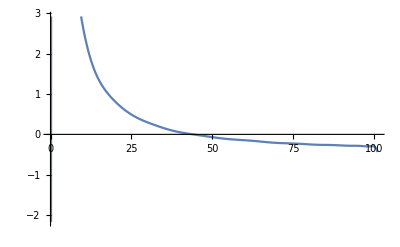

```mathematica
g1=Plot[f[x],{x,0,101}]
```

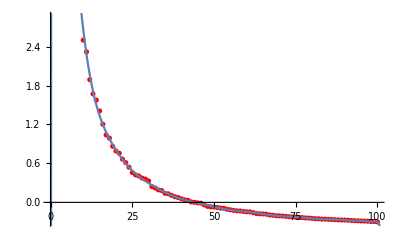

```mathematica
Show[{g0,g1}]
```